This shows how to call the connecting routine with Mathematica

First compile the source using 

cd Ultraspherical
mcc ultrasolve.tm UltrasphericalMathLink.cpp AdaptiveQR.cpp FilledBandedOperator.cpp UltrasphericalOperator.cpp Operator.cpp -o UltrasphericalMathLink


We can now install the compiled file:

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];
```

This installs UltrasphericalSolve[{a0,...,an}], which solves the ODE u’’ + (a0 T0(x) + ... + an Tn(x)) u = 0, u(-1) = 1, u(1) = 0.

```mathematica
a=Exp[#]&//Fun;b=AiryAi[#]&//Fun;f=Cos[Cos[#]]&//Fun;
```

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];U=PoissonSolve[a//DCT];
```

```mathematica
Length/@U
```

{45,47,49,50,52,53,54,55,56,58,59,60,61,62,63,64,64,63,61,51,34,25}

```mathematica
Norm/@U
```

{0.443146,0.168858,0.0562805,0.0216882,0.0100417,0.00530446,0.00306358,0.00187021,0.001166,0.000706011,0.000368887,0.0000884137,2.59598×10^-7,2.12297×10^-9,6.03597×10^-10,2.41096×10^-11,1.26924×10^-12,1.21039×10^-15,1.47859×10^-15,4.01427×10^-18,4.39824×10^-24,2.58793×10^-35}

```mathematica
U⟦1⟧
```

```mathematica
Norm/@U
```

{0.443146,0.168858,0.0562805,0.0216882,0.0100417,0.00530446,0.00306358,0.00187021,0.001166,0.000706011,0.000368887,0.0000884132,2.596×10^-7,2.12306×10^-9,6.03598×10^-10,2.41096×10^-11,1.26924×10^-12,1.21041×10^-15,1.47859×10^-15,4.01443×10^-18,4.02578×10^-24,2.58793×10^-35}

```mathematica
Last/@U
```

{4.90713×10^-31,3.59567×10^-35,9.982×10^-40,1.81486×10^-44,8.67035×10^-49,8.65897×10^-54,2.79094×10^-58,7.81316×10^-63,1.91763×10^-67,4.14313×10^-72,7.88908×10^-77,1.32347×10^-81,1.95339×10^-86,2.61791×10^-91,3.115×10^-96,3.16051×10^-101,1.43476×10^-104,-4.79321×10^-111,-9.42364×10^-113,1.09436×10^-113,-1.58347×10^-111,-3.42645×10^-114}

```mathematica
U⟦1⟧
```

{-9.43102×10^-7,-3.76794×10^-6,-8.41655×10^-6,-0.0000146485,-0.0000218604,-0.0000289613,-0.000034486,-0.0000370631,-0.000036047,-0.0000318577,-0.0000257455,-0.0000191759,-0.000013277,-8.61707×10^-6,-5.28194×10^-6,-3.07704×10^-6,-1.71214×10^-6,-9.1335×10^-7,-4.68385×10^-7,-2.31343×10^-7,-1.10195×10^-7,-5.06646×10^-8,-2.24987×10^-8,-9.65438×10^-9,-4.00461×10^-9,-1.6062×10^-9,-6.23103×10^-10,-2.33853×10^-10,-8.49262×10^-11,-2.9849×10^-11,-1.01545×10^-11,-3.34385×10^-12,-1.06577×10^-12,-3.28705×10^-13,-9.80591×10^-14,-2.82751×10^-14,-7.87279×10^-15,-2.1142×10^-15,-5.47075×10^-16,-1.36485×10^-16,-3.30156×10^-17,-7.89337×10^-18,-1.95561×10^-18,-5.44523×10^-19,-1.81865×10^-19,-7.07726×10^-20,-2.91335×10^-20,-1.16492×10^-20,-4.16773×10^-21,-9.31685×10^-22,-1.04221×10^-55,1.46484×10^-56,-8.17048×10^-58,2.27527×10^-59,-3.51619×10^-61,3.15067×10^-63,-1.65034×10^-65,4.94676×10^-68,-8.0263×10^-71,6.32203×10^-74,-1.94088×10^-77,1.32347×10^-81}

```mathematica
U//Length
```

22

```mathematica
X=BlockDiagonalMatrix[{({{0, 0}, {0, 0}}),PadRight[U,{U//Length,Length/@U//Max}]}];
```

```mathematica
X//ArrayPlot
```

-Graphics-

```mathematica
n=50;
```

```mathematica
DerivativeMatrix[2,n].X.ConversionMatrix[2,n]ᵀ+ConversionMatrix[2,n].X.DerivativeMatrix[2,n]ᵀ//Chop//MatrixForm
```

(1.25822 | 1.99596 | -0.022197 | -0.183192 | -0.0152129 | -0.00343752 | -0.00139316 | -0.000676797 | -0.000360378 | -0.000203038 | -0.000118271 | -0.0000699502 | -0.0000413926 | -0.0000242234 | -0.0000138975 | -7.76883×10^-6 | -4.21431×10^-6 | -2.21302×10^-6 | -1.12348×10^-6 | -5.51117×10^-7 | -2.61222×10^-7 | -1.1967×10^-7 | -5.30094×10^-8 | -2.2716×10^-8 | -9.42188×10^-9 | -3.78421×10^-9 | -1.47241×10^-9 | -5.55204×10^-10 | -2.02946×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.264809 | 0.661482 | 0.151037 | -0.068038 | -0.0207615 | -0.00448877 | -0.00126356 | -0.000499257 | -0.00024182 | -0.000130246 | -0.0000741492 | -0.0000433159 | -0.0000254561 | -0.0000148404 | -8.49732×10^-6 | -4.74593×10^-6 | -2.57409×10^-6 | -1.3521×10^-6 | -6.86813×10^-7 | -3.37163×10^-7 | -1.59945×10^-7 | -7.33389×10^-8 | -3.25165×10^-8 | -1.39472×10^-8 | -5.79031×10^-9 | -2.32782×10^-9 | -9.06599×10^-10 | -3.42183×10^-10 | -1.25202×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.12537 | -0.196095 | 0.074904 | 0.00863439 | -0.00818896 | -0.00417192 | -0.00140308 | -0.000481923 | -0.000194474 | -0.0000916907 | -0.000048016 | -0.0000266768 | -0.0000152209 | -8.72484×10^-6 | -4.95113×10^-6 | -2.75456×10^-6 | -1.49304×10^-6 | -7.85358×10^-7 | -4.00004×10^-7 | -1.97044×10^-7 | -9.38379×10^-8 | -4.32037×10^-8 | -1.92359×10^-8 | -8.28577×10^-9 | -3.45449×10^-9 | -1.39466×10^-9 | -5.45474×10^-10 | -2.0676×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0310306 | -0.0746437 | 0.000315841 | 0.0117833 | 0.00208194 | -0.00130807 | -0.00104066 | -0.00048366 | -0.000204519 | -0.0000905923 | -0.0000436251 | -0.0000225927 | -0.0000122695 | -6.81896×10^-6 | -3.80478×10^-6 | -2.10211×10^-6 | -1.13911×10^-6 | -6.01638×10^-7 | -3.08503×10^-7 | -1.53231×10^-7 | -7.36356×10^-8 | -3.42214×10^-8 | -1.5381×10^-8 | -6.68753×10^-9 | -2.814×10^-9 | -1.14645×10^-9 | -4.52439×10^-10 | -1.73029×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00889654 | -0.0173664 | -0.00890642 | 0.00154362 | 0.00258915 | 0.000659635 | -0.000231513 | -0.000293453 | -0.000176971 | -0.0000899416 | -0.0000445807 | -0.0000226978 | -0.0000119879 | -6.51151×10^-6 | -3.58545×10^-6 | -1.9732×10^-6 | -1.07273×10^-6 | -5.71151×10^-7 | -2.96073×10^-7 | -1.4888×10^-7 | -7.24711×10^-8 | -3.41165×10^-8 | -1.55281×10^-8 | -6.8343×10^-9 | -2.90973×10^-9 | -1.19896×10^-9 | -4.78374×10^-10 | -1.84906×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0031652 | -0.0039501 | -0.00401193 | -0.00140769 | 0.000600901 | 0.000720296 | 0.000237897 | -0.0000359232 | -0.00008958 | -0.0000678282 | -0.0000404499 | -0.0000224102 | -0.0000122567 | -6.7529×10^-6 | -3.75029×10^-6 | -2.0827×10^-6 | -1.14489×10^-6 | -6.17369×10^-7 | -3.24378×10^-7 | -1.65338×10^-7 | -8.15476×10^-8 | -3.88725×10^-8 | -1.79026×10^-8 | -7.96704×10^-9 | -3.42748×10^-9 | -1.42623×10^-9 | -5.74368×10^-10 | -2.23987×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00136229 | -0.00119796 | -0.001341 | -0.00103316 | -0.000248607 | 0.000229156 | 0.000239064 | 0.0000955181 | 5.74751×10^-7 | -0.0000284049 | -0.0000269145 | -0.0000185805 | -0.0000114725 | -6.78578×10^-6 | -3.94048×10^-6 | -2.25674×10^-6 | -1.2697×10^-6 | -6.97571×10^-7 | -3.72287×10^-7 | -1.92318×10^-7 | -9.59731×10^-8 | -4.62275×10^-8 | -2.14901×10^-8 | -9.64536×10^-9 | -4.1821×10^-9 | -1.75291×10^-9 | -7.10732×10^-10 | -2.78938×10^-10 | -1.06025×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000667523 | -0.000488017 | -0.000467263 | -0.000474434 | -0.000293497 | -0.0000388352 | 0.0000943316 | 0.0000916108 | 0.0000424847 | 5.90513×10^-6 | -8.86382×10^-6 | -0.000011031 | -8.82765×10^-6 | -6.0575×10^-6 | -3.85673×10^-6 | -2.34307×10^-6 | -1.37044×10^-6 | -7.72978×10^-7 | -4.20234×10^-7 | -2.20068×10^-7 | -1.10989×10^-7 | -5.39235×10^-8 | -2.52524×10^-8 | -1.14074×10^-8 | -4.97506×10^-9 | -2.09648×10^-9 | -8.54283×10^-10 | -3.36846×10^-10 | -1.286×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000352523 | -0.000236157 | -0.000189363 | -0.000199715 | -0.000173969 | -0.0000883005 | 1.40754×10^-6 | 0.0000432715 | 0.0000401089 | 0.0000208205 | 5.04058×10^-6 | -2.72583×10^-6 | -4.8883×10^-6 | -4.48456×10^-6 | -3.33535×10^-6 | -2.22072×10^-6 | -1.37328×10^-6 | -8.01763×10^-7 | -4.45544×10^-7 | -2.36738×10^-7 | -1.20623×10^-7 | -5.90578×10^-8 | -2.783×10^-8 | -1.26395×10^-8 | -5.539×10^-9 | -2.34451×10^-9 | -9.59336×10^-10 | -3.79757×10^-10 | -1.45522×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000189961 | -0.000122092 | -0.0000865649 | -0.0000863435 | -0.0000862106 | -0.0000647316 | -0.0000259646 | 7.55726×10^-6 | 0.0000212636 | 0.0000184109 | 9.63055×10^-6 | 2.28445×10^-6 | -1.57916×10^-6 | -2.74829×10^-6 | -2.54344×10^-6 | -1.89103×10^-6 | -1.24369×10^-6 | -7.52435×10^-7 | -4.27069×10^-7 | -2.29909×10^-7 | -1.18165×10^-7 | -5.82241×10^-8 | -2.75804×10^-8 | -1.25844×10^-8 | -5.53905×10^-9 | -2.3545×10^-9 | -9.67415×10^-10 | -3.84499×10^-10 | -1.47912×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000093168 | -0.0000608927 | -0.0000458587 | -0.000051689 | -0.0000647638 | -0.0000742517 | -0.0000734367 | -0.0000640355 | -0.0000524352 | -0.0000426896 | -0.0000348291 | -0.0000276009 | -0.0000206037 | -0.0000142973 | -9.22268×10^-6 | -5.56366×10^-6 | -3.16219×10^-6 | -1.70498×10^-6 | -8.77021×10^-7 | -4.32318×10^-7 | -2.0493×10^-7 | -9.36695×10^-8 | -4.13737×10^-8 | -1.7691×10^-8 | -7.33362×10^-9 | -2.9508×10^-9 | -1.15355×10^-9 | -4.38464×10^-10 | -1.62128×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0000215591 | -0.000019457 | -0.0000279656 | -0.0000497927 | -0.0000814068 | -0.000115704 | -0.000142429 | -0.000153218 | -0.000146208 | -0.000125892 | -0.000099371 | -0.0000728154 | -0.0000499854 | -0.0000323535 | -0.0000198408 | -0.0000115739 | -6.44443×10^-6 | -3.43548×10^-6 | -1.75806×10^-6 | -8.6556×10^-7 | -4.10768×10^-7 | -1.88197×10^-7 | -8.33507×10^-8 | -3.57233×10^-8 | -1.48293×10^-8 | -5.96662×10^-9 | -2.3282×10^-9 | -8.81433×10^-10 | -3.23876×10^-10 | -1.15529×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.74598×10^-7 | -4.30341×10^-6 | -0.000012694 | -0.000027388 | -0.0000482921 | -0.0000726939 | -0.0000951409 | -0.00010935 | -0.000111379 | -0.000101607 | -0.0000840116 | -0.0000637241 | -0.000044846 | -0.0000295708 | -0.0000184172 | -0.0000109031 | -6.16478×10^-6 | -3.34089×10^-6 | -1.73982×10^-6 | -8.72287×10^-7 | -4.21632×10^-7 | -1.9669×10^-7 | -8.86258×10^-8 | -3.85965×10^-8 | -1.62546×10^-8 | -6.6228×10^-9 | -2.6116×10^-9 | -9.97056×10^-10 | -3.68642×10^-10 | -1.32032×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.34811×10^-7 | -8.07431×10^-7 | -2.40465×10^-6 | -5.23139×10^-6 | -9.36842×10^-6 | -0.0000144803 | -0.000019706 | -0.0000238264 | -0.0000257486 | -0.0000250325 | -0.0000220695 | -0.0000178083 | -0.000013279 | -9.23431×10^-6 | -6.03787×10^-6 | -3.73741×10^-6 | -2.20203×10^-6 | -1.24003×10^-6 | -6.69434×10^-7 | -3.47213×10^-7 | -1.73285×10^-7 | -8.33079×10^-8 | -3.86121×10^-8 | -1.72644×10^-8 | -7.45072×10^-9 | -3.10504×10^-9 | -1.2501×10^-9 | -4.86413×10^-10 | -1.82989×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.56788×10^-10 | -2.14227×10^-9 | -6.38243×10^-9 | -1.38915×10^-8 | -2.49024×10^-8 | -3.85717×10^-8 | -5.27052×10^-8 | -6.41901×10^-8 | -7.02109×10^-8 | -6.95353×10^-8 | -6.29449×10^-8 | -5.26076×10^-8 | -4.09944×10^-8 | -3.00467×10^-8 | -2.08665×10^-8 | -1.38105×10^-8 | -8.74987×10^-9 | -5.32404×10^-9 | -3.11843×10^-9 | -1.76106×10^-9 | -9.59849×10^-10 | -5.05217×10^-10 | -2.56869×10^-10 | -1.26151×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.28617×10^-10 | 2.81503×10^-10 | 4.68169×10^-10 | 6.43679×10^-10 | 7.61811×10^-10 | 7.96775×10^-10 | 7.51256×10^-10 | 6.49008×10^-10 | 5.20711×10^-10 | 3.92394×10^-10 | 2.8032×10^-10 | 1.91264×10^-10 | 1.25374×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.18574×10^-10 | 1.60838×10^-10 | 1.92546×10^-10 | 2.06196×10^-10 | 2.00114×10^-10 | 1.78175×10^-10 | 1.47188×10^-10 | 1.1395×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

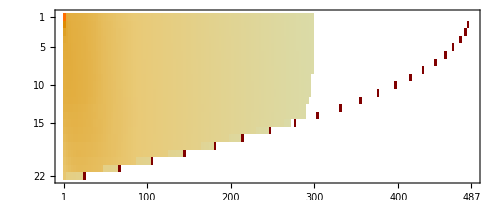

```mathematica
U//Abs//MatrixPlot
```

```mathematica
"3"
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},{10}]
```

{-0.247874,-0.594583,2.30122,-0.419138,-0.0549055,0.0139635,0.00157663,-0.0002374,-0.000019297,-5.1177×10^-6,-4.89701×10^-7,2.82999×10^-7,4.26803×10^-8,-1.91736×10^-9,-9.51222×10^-10,-1.61885×10^-10,-1.14567×10^-11,3.43466×10^-12,9.12297×10^-13,7.22144×10^-14,-6.22647×10^-15,-3.03866×10^-15,-4.84882×10^-16,-1.79416×10^-17,8.10583×10^-18,1.95887×10^-18,2.08444×10^-19,-3.09281×10^-21,-3.06823×10^-19,-6.54872×10^-20,-8.98754×10^-21,-9.42825×10^-22,-8.00475×10^-23,-6.26197×10^-24,-3.77888×10^-25,-1.38445×10^-26,-1.87504×10^-27,-7.52495×10^-29,1.03076×10^-29,-8.0746×10^-31,-2.25679×10^-32,1.04336×10^-32,-7.76054×10^-34,-7.59212×10^-35,1.08032×10^-36}

```mathematica
?ToCSeries
```

Information::notfound: Symbol "ToCSeries" not found.

```mathematica
<<Ultraspherical`
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},ConversionMatrix[2,f//Length].(f//DCT)]
```

{1.77843,-1.0268,0.233404,0.0275852,-0.0122066,-0.000798944,0.000370531,0.000015407,-2.01162×10^-6,-3.11702×10^-7,-2.02547×10^-7,-1.10707×10^-8,6.32145×10^-9,8.88606×10^-10,8.24681×10^-12,-1.44745×10^-11,-4.24162×10^-12,-4.27638×10^-13,4.81526×10^-14,1.80552×10^-14,2.24544×10^-15,3.40248×10^-17,-5.18279×10^-17,-1.13558×10^-17,-9.29563×10^-19,7.75477×10^-20,3.64148×10^-20,5.63303×10^-21,1.64602×10^-20,-3.68893×10^-21,-1.13701×10^-21,-1.81274×10^-22,-2.08773×10^-23,-1.86013×10^-24,-1.55244×10^-25,-1.05182×10^-26,-3.70396×10^-28,-4.54916×10^-29,-3.02197×10^-30,2.48427×10^-31,-1.42174×10^-32,-1.31498×10^-33,2.67939×10^-34,-1.05126×10^-35,-1.96762×10^-36}

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},(f//DCT)]//InverseDCT//Fun;
```

```mathematica
n=u//Length;
```

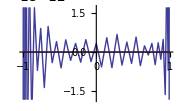

```mathematica
u''+SetLength[a,n] u'+SetLength[b,n] u-SetLength[f,n]
```

```mathematica
ConversionMatrix[1->2,n]//MatrixForm
```

(1 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | -1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | 0 | -1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/7 | 0 | -1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | -1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | -1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/10 | 0 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | -1/13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/12 | 0 | -1/14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/13 | 0 | -1/15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/14 | 0 | -1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/15 | 0 | -1/17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 0 | -1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/17 | 0 | -1/19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | -1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/19 | 0 | -1/21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | -1/22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/21 | 0 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/22 | 0 | -1/24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/23 | 0 | -1/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/24 | 0 | -1/26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/25 | 0 | -1/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/26 | 0 | -1/28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/27 | 0 | -1/29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/28 | 0 | -1/30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/29 | 0 | -1/31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/30 | 0 | -1/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/31 | 0 | -1/33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/32 | 0 | -1/34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/33 | 0 | -1/35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/34 | 0 | -1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/35 | 0 | -1/37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | -1/38 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/37 | 0 | -1/39 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/38 | 0 | -1/40 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/39 | 0 | -1/41 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/40 | 0 | -1/42 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/41 | 0 | -1/43 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/42 | 0 | -1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/43 | 0 | -1/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45)

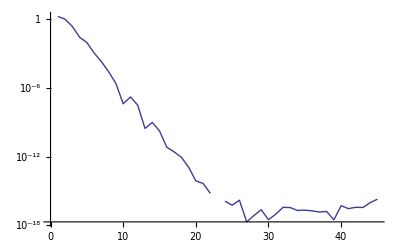

```mathematica
u//DCTPlot
```

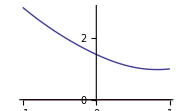

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},f//DCT]//InverseDCT//Fun
```

```mathematica
Timing[a=UltrasphericalSolve[al=Range[0,4]]]
```

{0.00018,{0.488604,-0.502508,-0.0194546,0.0167421,0.0405325,-0.0206584,-0.00982441,0.00685922,0.000293126,-0.000581009,-0.000166953,0.000169843,0.0000164067,-0.000025738,3.29936×10^-7,2.2736×10^-6,6.57296×10^-8,-3.98994×10^-7,1.00771×10^-8,4.19434×10^-8,-3.19253×10^-9,-3.41296×10^-9,3.22838×10^-10,4.41094×10^-10,-4.55209×10^-11,-3.66263×10^-11,5.19088×10^-12,2.66422×10^-12,-5.04701×10^-13,-2.78731×10^-13,4.81037×10^-14,1.93057×10^-14,-4.16034×10^-15,-1.24332×10^-15,3.59411×10^-16,1.11436×10^-16,-2.78233×10^-17,-6.57982×10^-18,2.04436×10^-18,3.71188×10^-19,-1.5747×10^-19,-2.97359×10^-20,1.05053×10^-20,1.49154×10^-21,-6.02003×10^-20,-6.4449×10^-21,4.37554×10^-21,5.22437×10^-22,-2.47318×10^-22,-3.10738×10^-23}}

We can compare the error with Mathematica:

```mathematica
<<Ultraspherical`
```

```mathematica
n=a//Length;Timing[amat=LinearSolve[Join[{DirichletOperator[-1]⟦1,;;n⟧,DirichletOperator[1]⟦1,;;n⟧},DerivativeMatrix[2,n]+ConversionMatrix[2,n].MultiplicationMatrix[al,n] //Most//Most],PadRight[{1,0},n]];]
```

{0.01878,Null}

```mathematica
amat-a//Norm
```

2.01477×10^-16